## Load data

```mathematica
SetDirectory@NotebookDirectory[];
data=Import["supplementary_data.xlsx"];
docs=data[[3]]; (*COLUMN NAMES: {"id","original","place","Latitude","Longitude","year","month","other","vydavatel","vydavatel2"}*)
docs[[2;;All,5]]=Round@docs[[2;;All,5]]; (*round years*)
docList=docs[[2;;All,1]]; (* document names only *)
issuerList=Union[docs[[2;;All,-2]]];  (* issuer names only *)
yearList=Union[docs[[2;;All,5]]];
missing={#,0}&/@Complement[Range[yearList[[1]],yearList[[-1]]],yearList];
(* years without any documents *)
funcList=data[[6,2;;All]]; (* function names only *)

incid=data[[4]]/.""->0;
names=DeleteCases[Drop[incid[[All,2]],1],0];
incid=incid[[2;;Length@names+1,Flatten[Position[incid[[1]],#]&/@docList]]];(* Same ordering as in docs *)
incidFunc=incid;
incid=incid/._String->1;
incid=SparseArray[incid,{Length@names,Length@docList}];
```

### Functions

```mathematica
makeNet[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam,g},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
adjNam=ArrayRules@SparseArray[incid[[All,selectPos]].Transpose[incid[[All,selectPos]]]-SparseArray@IdentityMatrix[Length[names]],Automatic,0]; (* make adjacency from incidence matrix *)
adjNam=DeleteCases[adjNam,PatternSequence[{x_,x_}->_]];
AppendTo[adjNam,{_,_}->∞];
g=WeightedAdjacencyGraph[SparseArray[adjNam,Length[names]]];
{adjNam,g}
];
```

```mathematica
makeNodes[minYear_,maxYear_]:=Module[{selectDoc,selectPos,adjNam},
selectDoc=Cases[docs,{x_,_,_,_,year_,_,_,_}:>x/;minYear≤year≤ maxYear];
selectPos=Flatten[Position[docList,#]&/@selectDoc];
adjNam=ArrayRules@SparseArray[incid[[All,selectPos]],Automatic,0];
Union@adjNam[[All;;-2,1,1]]
];
```

### Make networks

```mathematica
wholeNet=makeNet[yearList[[1]],yearList[[-1]]];
nn=VertexCount[wholeNet[[2]]];
ee=EdgeCount[wholeNet[[2]]];
```

```mathematica
(* This one takes some time *)
nets=ParallelTable[makeNet[year,year],{year,yearList}];
```

### Graphics

```mathematica
marker1=Graphics[{EdgeForm[Directive[Thick,RGBColor[0,0,0],Opacity[1]]],White,Disk[]},ImageSize->14];
marker2=Graphics[{EdgeForm[Directive[Thick,RGBColor[1,0,0],Opacity[1]]],RGBColor[1,1,1],Triangle[{{0,0},{1,0},{1/2,√3/2}}]},ImageSize->15];
marker3=Graphics[{RGBColor[0,0,1],Polygon[{{1/2,0},{0,1/2},{1/2,1},{1,1/2}}]},ImageSize->15];
```

```mathematica
(* Overlays for the timeline figures *)
shade=ListPlot[Transpose@{{1248+7/12,1249+8/12},ConstantArray[ee,2]},Joined->True,Filling->Bottom,FillingStyle->Directive[Red,Opacity[0.5]]];
line=ListPlot[{{1230,ee},{1253,ee}},Filling->0,FillingStyle->Directive[Black,Dashed]];
line1=ListPlot[{{1230+0.5,ee},{1253+0.5,ee}},Filling->0,FillingStyle->Directive[Black,Dashed]];
```

## Timelines

### Compute timelines

```mathematica
(* The number of STABLE LINKS/WEIGHTS*)
tab=ParallelTable[
{Length@Drop[Intersection[nets[[y]][[1,All,1]],nets[[y-1]][[1,All,1]]],-1]/2,
Length@Drop[Intersection[nets[[y]][[1,All]],nets[[y-1]][[1,All]]],-1]/2}
,{y,2,Length@yearList}];
(*CDF OF LINKS/VERTICES/WEIGHTS => DIFFERENCES=NEW LINKS/...*)
tab1=ParallelTable[
temp=makeNet[yearList[[1]],year];
{EdgeCount[temp[[2]]],VertexCount[temp[[2]]]-Count[DegreeCentrality[temp[[2]]],0]}
,{year,yearList}];
(*LINKS/VERTICES/WEIGHTS EXISTING IN A GIVEN YEAR*)
tab2=ParallelTable[
temp=net;
{EdgeCount[temp[[2]]],VertexCount[temp[[2]]]-Count[DegreeCentrality[temp[[2]]],0],Total@Drop[temp[[1,All,2]],-1]/2(* EdgeCount does not take weight into account; /2 because networks are symmetric *)}
,{net,nets}];
(*CONNECTED COMPONENTS EXISTING IN A GIVEN YEAR*)
comp1=ParallelTable[
Length@ConnectedComponents[Subgraph[nets[[i,2]],makeNodes[yearList[[i]],yearList[[i]]]]]
,{i,1,Length@yearList}];
```

```mathematica
raster=ParallelTable[
temp=nets[[i]];
{yearList[[i]],#[[1]]}->#[[2]]&/@Drop[Tally@Flatten@temp[[1,All,1]],-1]
,{i,1,Length@yearList}];
raster=Flatten[raster,1];
raster=Transpose@SparseArray@raster/2;
```

### Plot: documents, vertices, edges, connected components

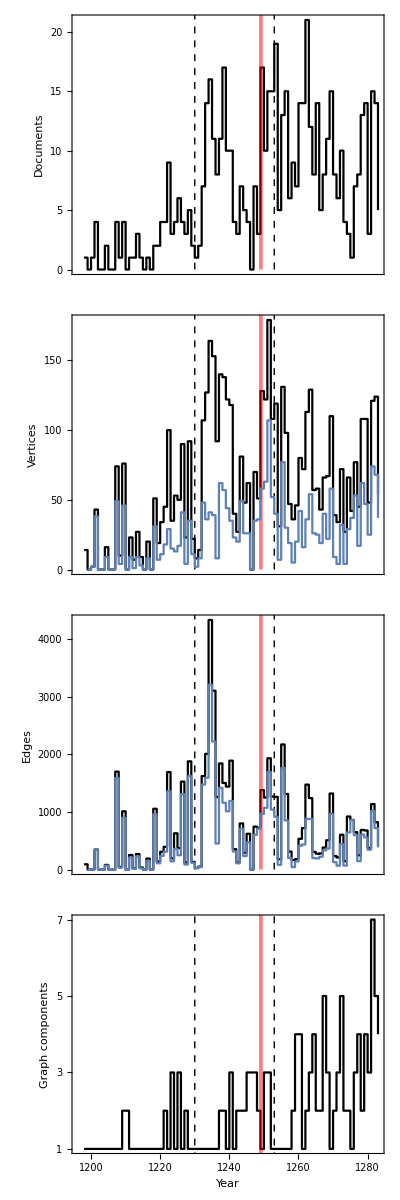

```mathematica
Grid[{{Show[{ListPlot[Sort[Transpose[{yearList,Length@Position[docs,{__,#,__}]&/@yearList}]~Join~missing],Joined->True,InterpolationOrder->0,PlotStyle->Black,Frame->True,PlotRange->{0,Automatic},AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Table[{t,t,{0.01,0}},{t,0,20,5}],Table[{t,"",{0.01,0}},{t,0,20,5}]},{Table[{t,"",{0.01,0}},{t,1200,1280,20}]~Join~Table[{t,"",{0.005,0}},{t,1200,1280,5}],Automatic}},FrameLabel->{None,Style["Documents","Arial",14,Black]},ImageSize->Automatic->460,AspectRatio->1/3.5],shade,line}]},{
Show[{ListPlot[Sort[Transpose[{yearList,tab2[[All,2]]}]~Join~missing],Joined->True,InterpolationOrder->0,PlotStyle->Black,Frame->True,PlotRange->{0,Automatic},AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],
FrameTicks->{{Table[{t,t,{0.01,0}},{t,0,150,50}],Table[{t,"",{0.01,0}},{t,0,150,50}]},{Table[{t,"",{0.01,0}},{t,1200,1280,20}]~Join~Table[{t,"",{0.005,0}},{t,1200,1280,5}],Automatic}},FrameLabel->{None,Style["Vertices","Arial",14,Black]},ImageSize->Automatic->460,AspectRatio->1/3.5],shade,line,ListPlot[Sort[Transpose[{Drop[yearList,1],Differences@tab1[[All,2]]}]~Join~missing],Joined->True,InterpolationOrder->0]}]
},{
Show[{ListPlot[Sort[Transpose[{yearList,tab2[[All,1]]}]~Join~missing],Joined->True,InterpolationOrder->0,PlotStyle->Black,Frame->True,PlotRange->{0,Automatic},AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Table[{t,t,{0.01,0}},{t,0,4000,1000}],Table[{t,"",{0.01,0}},{t,0,4000,1000}]},{Table[{t,"",{0.01,0}},{t,1200,1280,20}]~Join~Table[{t,"",{0.005,0}},{t,1200,1280,5}],Automatic}},FrameLabel->{None,Style["Edges","Arial",14,Black]},ImageSize->Automatic->460,AspectRatio->1/3.5],shade,line,ListPlot[Sort[Transpose[{Drop[yearList,1],Differences@tab1[[All,1]]}]~Join~missing],Joined->True,InterpolationOrder->0]}]},
{
Show[{ListPlot[{Transpose@{yearList,comp1}},Joined->True,InterpolationOrder->0,PlotStyle->{Black},Frame->True,PlotRange->{1,Automatic},
AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Table[i,{i,1,7,2}],Table[{i,""},{i,1,7,2}]},{Automatic,Automatic}},FrameLabel->{Style["Year","Arial",12,Black],Style["Graph\ncomponents","Arial",14,Black]},ImageSize->Automatic->460,AspectRatio->1/6],shade,line}]}
},Spacings->{0,-0.2},Alignment->Right]
```

### Plot: stable edges

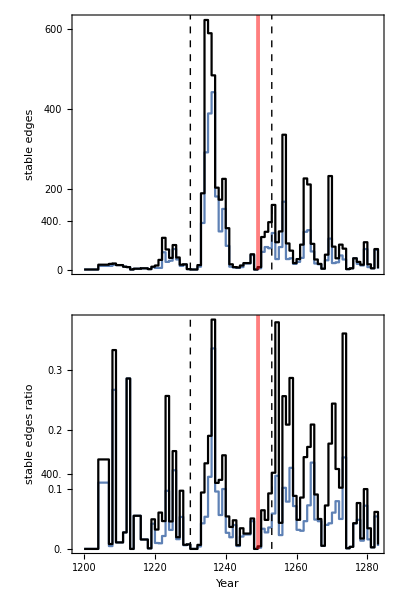

```mathematica
Grid[{
{Show[{ListPlot[Reverse@{Transpose@{Drop[yearList,1],tab[[All,1]]},
Transpose@{Drop[yearList,1],tab[[All,2]]}},Joined->True,InterpolationOrder->0,PlotStyle->{Automatic,Black},Frame->True,PlotRange->{0,All},AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Table[{t,t,{0.01,0}},{t,0,600,200}]~Join~Table[{t,"",{0.005,0}},{t,100,600,100}]~Join~{{120,Style["400.",White],0}},Table[{t,"",{0.01,0}},{t,0,600,200}]~Join~Table[{t,"",{0.005,0}},{t,100,600,100}]},{Table[{t,"",{0.01,0}},{t,1200,1280,20}]~Join~Table[{t,"",{0.005,0}},{t,1200,1280,5}],Automatic}},FrameLabel->{None,Style["stable edges","Arial",14,Black]},ImageSize->505,AspectRatio->1/3],shade,line}]},
{Show[{ListPlot[Reverse@{Transpose@{Drop[yearList,1],tab[[All,1]]/tab2[[2;;All,1]]},
Transpose@{Drop[yearList,1],tab[[All,2]]/tab2[[2;;All,3]]}},Joined->True,InterpolationOrder->0,PlotStyle->{Automatic,Black},Frame->True,PlotRange->{0,All},AxesOrigin->0, FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameTicks->{{Table[{t,t,{0.01,0}},{t,0,0.4,0.1}]~Join~Table[{t,"",{0.005,0}},{t,0.05,0.4,0.1}]~Join~{{0.125,Style["400.",White],0}},Table[{t,"",{0.01,0}},{t,0,0.4,0.1}]~Join~Table[{t,"",{0.005,0}},{t,0.05,0.4,0.1}]},{Automatic,Automatic}},FrameLabel->{Style["Year","Arial",12,Black],Style["stable edges ratio","Arial",14,Black]},ImageSize->505,AspectRatio->1/3],shade,line}]}
},Spacings->{0,-0.2}]
```

### Raster plot

```mathematica
mp=MatrixPlot[DeleteCases[Reverse[Sort[Normal[raster]]][[All,1230;;1259]],ConstantArray[0,31]],ImagePadding->0,Frame->False,ColorFunction->(ColorData["BeachColors"][(1.-#/140)^2]&),ColorFunctionScaling->False,AspectRatio->1,ImageSize->500,PlotRange->{Automatic,Automatic,{0,140}}];
bg={Texture[mp],Polygon[{{{1229.5,-0.6},{1260.5,-0.6},{1260.5,1},{1229.5,1}}},VertexTextureCoordinates->({{0,0},{1,0},{1,1},{0,1}})]};
Show[{ListPlot[Transpose@{{1248,1250},ConstantArray[2,2]},Joined->False,Filling->Bottom,FillingStyle->Directive[Red,Opacity[0.5]],Prolog->bg,AspectRatio->1,ImageSize->470,PlotRange->{{1230,1260},{0,1}},Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],FrameTicksStyle->Directive[12,"Arial",Black],FrameLabel->{None(*Style["Year","Arial",12,Black]*),Style["noblemen","Arial",14,Black]},FrameTicks->{{None,None},{Automatic,Automatic}}],line1}]
frame[legend_]:=Framed[legend,FrameStyle->Black,FrameMargins->0];
BarLegend[{(ColorData["BeachColors"][(1.-#/140)^2]&),{0,140}},LabelStyle->Directive[12,"Arial",Black],LegendLabel->"Edges",LegendMarkerSize->400,LegendFunction->frame]
```

-Graphics-